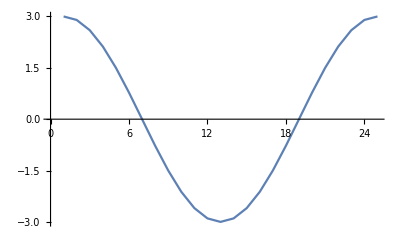

```mathematica
ListLinePlot[Table[Total[{E^(-I t)/2,E^(-I t),0,E^(I t),E^(I t)/2}]/.t-> t2//N,{t2,0,2Pi,Pi/12}]]
```

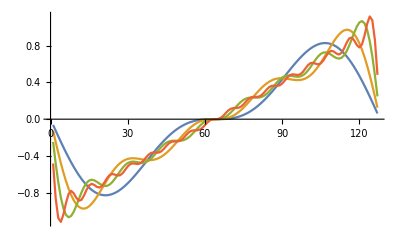

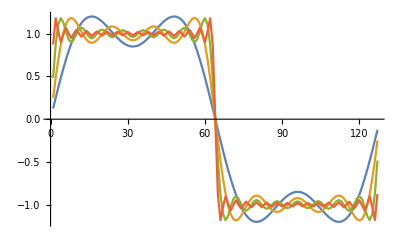

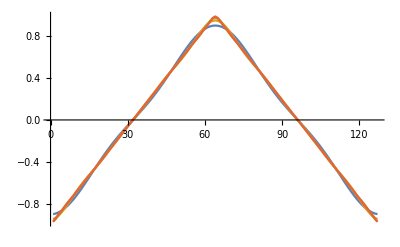

```mathematica
sr:=128;
harmonicsList:={2,4,8,16};
sawFouriers:=Table[Table[If[n==0,0,(-1)^n Exp[-I 2Pi n t]/(n Pi)],{n,-harmonics,harmonics}],{harmonics,harmonicsList}];
sawWaves:=Im@Table[Total@(#/.t->t2//N),{t2,-.5+1/sr,.5-1/sr,1/sr}]&/@sawFouriers;
sqrFouriers:=Table[Table[If[n==0||EvenQ[n],0,2Exp[-I 2Pi n t]/(n Pi)],{n,-2harmonics,2harmonics}],{harmonics,harmonicsList}];
sqrWaves:=Im@Table[Total@(#/.t->t2//N),{t2,-.5+1/sr,.5-1/sr,1/sr}]&/@sqrFouriers;
triFouriers:=Table[Table[If[n==0||EvenQ[n],0,4Exp[-I 2Pi n t]/(n^2 Pi^2)],{n,-2harmonics,2harmonics}],{harmonics,harmonicsList}];
triWaves:=Re@Table[Total@(#/.t->t2//N),{t2,-.5+1/sr,.5-1/sr,1/sr}]&/@triFouriers;
ListLinePlot[sawWaves]
ListLinePlot[sqrWaves]
ListLinePlot[triWaves]
```